```mathematica
(*Compute the repo root from the notebook location*)repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
URoots[N[2,100]]
u0 = %[[4]]
```

{-0.25716617386463644393706302623770958083567636406323279490317435391000875677710996530673846256200111-0.14498540496176211586181447937960395873612907508198703648782573993296665019919773127762910090259482 ⅈ,-0.25716617386463644393706302623770958083567636406323279490317435391000875677710996530673846256200111+0.14498540496176211586181447937960395873612907508198703648782573993296665019919773127762910090259482 ⅈ,0.227203634857985759161254765346706290384224015255178461093477420691304642267091217742189796411130923,1.}

1.

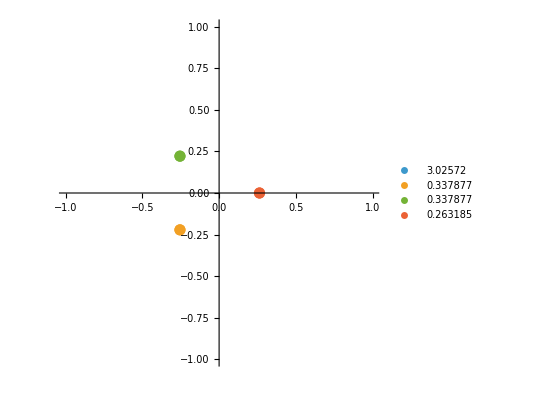

```mathematica
PlotURoots[N[1,100]]
```

```mathematica
b0 = NodalCurvebFrommu[N[2,100],u0]
```

-0.3819660112501051517954131656343618822796908201942371378645513772947395371810975502927927958106089

```mathematica
KerrDoranQ[b0]/(2Pi I)/.LiEval
```

0.0551589000381628983491141080294994227456724371824138676223158084267804417616716706244982779634919-0.584750831613469831108344339422151373612615844470651886935379744382584597390483314660777295412487 ⅈ

```mathematica
Pi/6//N
```

0.523599

```mathematica
u0 = URoots[N[1,100]][[4]]
```

0.263185269218743579065357060278145251896767028025740392847233274382509943322046211929710968647568384

```mathematica
b0 = NodalCurvebFrommu[1,u0]
```

-0.725149761049014866527565152463683894060127694261271422227462465469488441831473031269047768433093222+0.68859118789783872858051959055806444225530679847176447674205722337962953356247491861302058566205021 ⅈ

```mathematica
KerrDoranQ[b0]/(2Pi I)/.LiEval
```

0.184193533083328278281112707414501562738794690081586154019297422619339095109738026974056390832702-0.0833333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333 ⅈ

```mathematica
KerrDoranQ[b0]/.LiEval
```

0.523598775598298873077107230546583814032861566562517636829157432051302734381034833104672470890353+1.15732210074666531243235075733319062483391568725435034244705938558241669693977914018093542083103 ⅈ

```mathematica
Pi/6//N
```

0.523599

```mathematica
(Pi/6+t I)/(2Pi I)//Simplify
```

-ⅈ/12+t/(2 π)

## Monodromies of ODEs

```mathematica
DSolve[(z^2+1) f''[z]+2 z f'[z]==0,f[z],z]
```

{{f[z]→ArcTan[z] C[1]+C[2]}}

```mathematica
matA[z_]:={{0,1},{0,-2z/(z^2+1)}};
```

```mathematica
zpath[t_]:=I+10^-10 Exp[I t];
dzpath[t_]=D[zpath[t],t];
```

```mathematica
sol=NDSolveValue[{
Phi'[t]==dzpath[t]* matA[zpath[t]].Phi[t],
Phi[0]==IdentityMatrix[2]
},Phi,{t,0,2 Pi}];
```

```mathematica
Chop[sol[2Pi]]
```

{{1.,0.+6.28318×10^-10 ⅈ},{0,0.999999-1.7926×10^-7 ⅈ}}

```mathematica
ClearAll[companionMatrix];

(*Input:ode is an equation==0 or an expression;y is the function symbol;x is variable*)
companionMatrix[ode_,y_Symbol,x_Symbol]:=Module[{expr,n,uk,coeffs,an,rhs,bottomRow,A},(*normalize to an expression "==0"->lhs-rhs*)expr=ode/. Equal->Subtract//Expand;
(*detect order*)n=Max@Cases[expr,Derivative[k_][y][x]:>k,Infinity];
If[!IntegerQ[n]||n<1,Return[$Failed,Module]];
(*replace y^(k)(x) by u[k] to extract linear coefficients*)uk=Array[u,n+1,0];(*u[0]..u[n]*)coeffs=Coefficient[expr/. Join[{y[x]->u[0]},Table[Derivative[k][y][x]->u[k],{k,1,n}]],uk];
an=coeffs[[n+1]];
If[an===0,Return[$Failed,Module]];
(*y^(n)=-(a0 y+a1 y'+...+a_{n-1} y^(n-1))/an*)rhs=-(Most[coeffs].Most[uk])/an;
bottomRow=Table[Coefficient[rhs,u[j]],{j,0,n-1}];
(*build companion A(x) for U=(y,y',...,y^(n-1))^T*)A=ConstantArray[0,{n,n}];
Do[A[[i,i+1]]=1,{i,1,n-1}];
A[[n,;;]]=bottomRow;
{n,A} (*A is symbolic in x/parameters*)];
```

```mathematica
ClearAll[monodromyMatrix];
Options[monodromyMatrix]={WorkingPrecision->80,PrecisionGoal->40,AccuracyGoal->40,MaxSteps->Infinity,Method->"StiffnessSwitching"};

monodromyMatrix[ode_,y_Symbol,x_Symbol,x0_?NumericQ,r_?NumericQ,opts:OptionsPattern[]]:=Module[{n,A,Afun,z,zp,v,eqn,ic,sol,Mend},{n,A}=companionMatrix[ode,y,x];
If[{n,A}===$Failed,Return[$Failed]];
(*define A(z) with substitution;Evaluate to avoid repeated symbolic work*)Afun[zz_]:=Evaluate[A/. x->zz];
(*loop around x0*)z[t_]:=x0+r Exp[I t];
zp[t_]:=I r Exp[I t];
(*evolve flattened fundamental matrix v(t) in C^(n^2)*)v[t_]:=Array[vv,n^2][t];(*just a placeholder head*)eqn=Flatten@(D[ArrayReshape[v[t],{n,n}],t]==zp[t] (Afun[z[t]].ArrayReshape[v[t],{n,n}]));
(*convert matrix ODE to vector ODE*)eqn=Thread[D[v[t],t]==Flatten[zp[t] (Afun[z[t]].ArrayReshape[v[t],{n,n}])]];
ic=Thread[v[0]==Flatten[IdentityMatrix[n]]];
sol=NDSolveValue[Join[eqn,ic],v,{t,0,2 Pi},WorkingPrecision->OptionValue[WorkingPrecision],PrecisionGoal->OptionValue[PrecisionGoal],AccuracyGoal->OptionValue[AccuracyGoal],MaxSteps->OptionValue[MaxSteps],Method->OptionValue[Method]];
Mend=ArrayReshape[sol[2 Pi],{n,n}];
Chop[Mend,10^(-OptionValue[PrecisionGoal]/2)]];
```

```mathematica
ode=y''[x]+(1/x) y'[x]==0;

M=monodromyMatrix[ode,y,x,0.0,0.1,WorkingPrecision->80,PrecisionGoal->50,AccuracyGoal->50];

M//MatrixForm
```

ArrayReshape::listrp: List, SparseArray object, or structured array expected at position 1 in ArrayReshape[{vv[1],vv[2],vv[3],vv[4]}[t],{2,2}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Join::heads: Heads Equal and List at positions 1 and 2 are expected to be the same.

NDSolveValue::deqn: Equation or list of equations expected instead of Join[{0,0,0,0}[t]+{vv[1],vv[2],vv[3],vv[4]}'[t]==(0.+0.1 ⅈ) ⅇ^(ⅈ t) {{0,1},{0,-Power[«2»]}}.ArrayReshape[{vv[1],vv[2],vv[3],vv[4]}[t],{2,2}],{{vv[1],vv[2],vv[3],vv[4]}[0]==1,{«1»}[0]==0,«1»==0,«1»}] in the first argument Join[{0,0,0,0}[t]+{vv[1],vv[2],vv[3],vv[4]}'[t]==(0.+0.1 ⅈ) ⅇ^(ⅈ t) {{0,1},{0,-Power[«2»]}}.ArrayReshape[{vv[1],vv[2],vv[3],vv[4]}[t],{2,2}],{{vv[1],vv[2],vv[3],vv[4]}[0]==1,{«1»}[0]==0,«1»==0,«1»}].

ArrayReshape[NDSolveValue[Join[{0,0,0,0}[t]+{vv[1],vv[2],vv[3],vv[4]}'[t]==(0.+0.1 ⅈ) ⅇ^(ⅈ t) {{0,1},{0,-1/(0.+0.1 ⅇ^(ⅈ t))}}.ArrayReshape[{vv[1],vv[2],vv[3],vv[4]}[t],{2,2}],{{vv[1],vv[2],vv[3],vv[4]}[0]==1,{vv[1],vv[2],vv[3],vv[4]}[0]==0,{vv[1],vv[2],vv[3],vv[4]}[0]==0,{vv[1],vv[2],vv[3],vv[4]}[0]==1}],v$645207,{t,0,2 π},WorkingPrecision→80,PrecisionGoal→50,AccuracyGoal→50,MaxSteps→∞,Method→StiffnessSwitching][2 π],{2,2}]

```mathematica
Limit[(z-I){{0,1},{0,-2z/(z^2+1)}},z->I]
FullSimplify[MatrixPower[%,p],p∈PositiveIntegers]
```

{{0,0},{0,-1}}

{{0,0},{0,(-1)^p}}

```mathematica
DSolve[y''[z]+1/z y'[z]==0,y,z]
```

{{y→Function[{z},C[2]+C[1] Log[z]]}}

```mathematica
z[t_]:=N[I+10^-5 Exp[I t]];
```

```mathematica
zp[t_]=D[z[t],t];
```

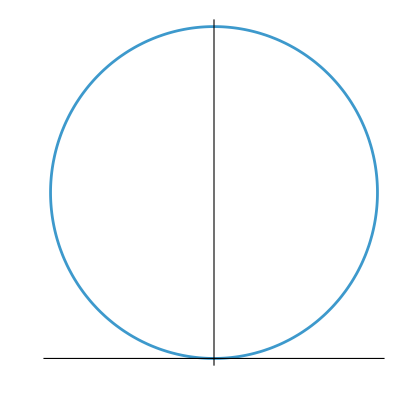

```mathematica
ParametricPlot[ReIm[z[t]],{t,0,2Pi},Ticks->None,ImageSize->Tiny]
```

```mathematica
NDSolve[{Phi'[t]==zp[t]/(z[t]^2+1), Phi[0]==0.}, Phi, {t,0,2Pi}]
Phi[2Pi]/.First[%]
```

{{Phi→InterpolatingFunction[…]}}

3.14159-4.66814×10^-9 ⅈ

```mathematica
NIntegrate[zp[t]/(z[t]^2+1), {t,0,2Pi}]
```

3.14159

```mathematica
2Pi I Limit[(z-I)1/(z^2+1), z->I]
```

π

```mathematica
DSolve[(z^2+1) f''[z]+2 z f'[z]==0,f[z],z]
```

{{f[z]→ArcTan[z] C[1]+C[2]}}

```mathematica
ClearAll[A,z,zPath,zPathD];
A[z_] = {{0,1},{0,-2z/(z^2+1)}}
zPath[t_]:=1.I+.01Exp[I t];
zPathD[t_]=D[zPath[t],t];NDSolve[{Phi'[t]==zPathD[t]*A[zPath[t]].Phi[t], Phi[0]==IdentityMatrix[2]}, Phi, {t,0,2Pi}]
Chop[Phi[2Pi]/.First[%]]
```

{{0,1},{0,-(2 z)/(1+z^2)}}

{{Phi→InterpolatingFunction[…]}}

{{1.,0.000314154+0.0628318 ⅈ},{0,1.+1.81392×10^-7 ⅈ}}

```mathematica
Limit[(z-I)A[z],z->I]
```

{{0,0},{0,-1}}

```mathematica
Series[1/2 ⅈ Log[1-ⅈ z]-1/2 ⅈ Log[1+ⅈ z], {z,I,3}]
```

1/2 ⅈ (Log[2]-Log[ⅈ (-ⅈ+z)])+(z-ⅈ)/4+1/16 ⅈ (z-ⅈ)^2-1/48 (z-ⅈ)^3+O[z-ⅈ]^4

```mathematica
Map[Expand,1/2 ⅈ (-Log[ⅈ (-ⅈ+z)]),Infinity]
```

-1/2 ⅈ Log[1+ⅈ z]

```mathematica
matA = {{0,1,0},{0,0,1/u},{0,(8+16 u-247 u^2-1860 u^3-2000 u^4-594 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)),(16+33 u-238 u^2-1656 u^3-1824 u^4-495 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5))}}
```

{{0,1,0},{0,0,1/u},{0,(8+16 u-247 u^2-1860 u^3-2000 u^4-594 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)),(16+33 u-238 u^2-1656 u^3-1824 u^4-495 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5))}}

```mathematica
Am1=Limit[u matA,u->0]
```

{{0,0,0},{0,0,1},{0,-1,-2}}

```mathematica
Eigenvalues[Am1]
```

{-1,-1,0}

```mathematica
Limit[matA-Am1/u,u->0]
%//JordanDecomposition;
MatrixForm/@%
```

{{0,1,0},{0,0,0},{0,1/8,1/8}}

{(1 | 0 | 0
0 | 1 | 0
0 | -1 | 1),(0 | 1 | 0
0 | 0 | 0
0 | 0 | 1/8)}

```mathematica
uRoots=u/.Solve[u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)==0,u]
```

{-8/9,0,,,,}

```mathematica
FullSimplify@Limit[(u-uRoots[[4]])matA,u->uRoots[[4]]]//JordanDecomposition
```

{{{0,0,1},{0,1/,0},{1,1,0}},{{-1,0,0},{0,0,0},{0,0,0}}}

```mathematica
D[ArcTan[z],z]
```

1/(1+z^2)

```mathematica
MLV//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 0 | 1 | 0
4 | 1 | 8 | 1)

## Picard Fuchs

```mathematica
{B3,B2,B1}={u (-128 m^4 u^4-16 m^3 u^2 (-4+9 u^3)+9 u^2 (-1+27 u^3)+8 m^2 (-1+45 u^3)+m u (-17+540 u^3)),-896 m^4 u^4+27 u^2 (-1+54 u^3)+24 m^2 (-1+84 u^3)+m (-50 u+3132 u^4)+m^3 (320 u^2-864 u^5),-1024 m^4 u^3-32 m^3 u (-8+27 u^3)+9 u (-1+162 u^3)+16 m (-1+189 u^3)+(4 m^2 (-2+465 u^3))/u};
```

```mathematica
FullSimplify[{B3,B2,B1}/.{m->1}].{Derivative[3][F][u],Derivative[2][F][u],Derivative[1][F][u]}
FullSimplify[%]
```

(-16-8/u+u (247+2 u (930+u (1000+297 u)))) F'[u]+(-24+u (-50+u (293+2 u (1008+u (1118+297 u))))) F''[u]+u (8+9 u) (-1+u (-1+u (8+u (36+11 u)))) F^(3)[u]

(-16-8/u+u (247+2 u (930+u (1000+297 u)))) F'[u]+(-24+u (-50+u (293+2 u (1008+u (1118+297 u))))) F''[u]+u (8+9 u) (-1+u (-1+u (8+u (36+11 u)))) F^(3)[u]

```mathematica
ZLV[{-1,0,0,0},T,0]
```

4 T^2

```mathematica
SameHalfPlaneQ[{}]:=True;
SameHalfPlaneQ[Zlist_List]:=If[AnyTrue[Zlist,#==0&],False,-Subtract@@MinMax[Arg[Zlist/Zlist[[1]]]]<Pi];
```

```mathematica
Options[QuiverDomain]={"Style"->LightBlue};
QuiverDomain[Coll_,psi_,m_,OptionsPattern[]]:={RegionPlot[(And@@Table[Re[Exp[-I psi]ZLV[Coll[[i]],{s,t},m]]<0,{i,Length[Coll]}])&&t>0,{s,-1.5,1.5},{t,0,1},PlotPoints->100,AspectRatio->1,PlotStyle->Flatten[{OptionValue["Style"],Opacity[.5]}]],RegionPlot[SameHalfPlaneQ[Table[ZLV[Coll[[i]],{s,t},m],{i,Length[Coll]}]],{s,-1.5,1.5},{t,0,1},PlotPoints->100,AspectRatio->1,BoundaryStyle->Directive[Dashed],PlotStyle->Flatten[{OptionValue["Style"],Opacity[.3]}]]};
```

```mathematica
FullSimplify[ComplexExpand[Im[ZLV[{r, dF, dB, ch2}, T, m]/.{T->s+I t}], {m}]]
```

t (dB+2 dF-8 r s-r Re[m])+Im[m] (-dB+dF-r s+r Re[m])

```mathematica
ZLV[{r, dF, dB, ch2}, {s,t}, m]
```

-ch2+s (dB+2 dF-4 r s)+4 r t^2+(-dB+dF) Re[m]+1/2 r (2 t Im[m]-Im[m]^2+Re[m] (-2 s+Re[m]))+ⅈ (t (dB+2 dF-8 r s-r Re[m])+Im[m] (-dB+dF-r s+r Re[m]))

```mathematica
FullSimplify[ZLV[{r, dF, dB, ch2}, T, m]/.{T->s+I t}]
```

-ch2+dB (-m+s+ⅈ t)+1/2 (2 dF+r (m-4 s-4 ⅈ t)) (m+2 s+2 ⅈ t)

```mathematica
PlotURoots[N[1,100]]
```

-Graphics-

```mathematica
M2p
```

{{1,0,0,0},{0,1,0,0},{0,1,3,1},{0,-2,-4,-1}}

```mathematica
Inverse[MonodromyFromSphericalTwist[-1,0]]==M2p
```

True

```mathematica
M1p//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-1/2 | 1 | 0 | 1
-1/2 | 1 | -1 | 1)

```mathematica
Inverse[MonodromyFromSphericalTwist[0,0].MonodromyFromSphericalTwist[0,1]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-1/2 | 1 | 0 | 1
-1/2 | 1 | -1 | 1)

## Roots of the indicial polynomial

```mathematica
{D[f[u],{u,3}],D[f[u],{u,2}],D[f[u],u]}/.{u->Exp[t]}
```

{f^(3)[ⅇ^t],f''[ⅇ^t],f'[ⅇ^t]}

```mathematica
SystemMatrix2[{{v1_,v2_},{v1p_,v2p_},{v1pp_,v2pp_}},el_,ur_]:={{1,(Log[ur]+1/3 Log[el]+v1)/(2 Pi I),(4 (π^2+6 v2)-3 (Log[el]^2+6 Log[el] (v1+Log[ur])+8 Log[ur] (2 v1+Log[ur])))/(24 π^2)},{0,-((I (1/ur+v1p))/(2 π)),-((8 v1-4 ur v2p+3 Log[el]+8 Log[ur]+ur v1p (3 Log[el]+8 Log[ur]))/(4 π^2 ur))},{0,-((I (-(1/ur^2)+v1pp))/(2 π)),(-8+8 v1-16 ur v1p+4 ur^2 v2pp+3 Log[el]-3 ur^2 v1pp Log[el]+8 Log[ur]-8 ur^2 v1pp Log[ur])/(4 π^2 ur^2)}};
```

```mathematica
TableForm[Expand/@SystemMatrix2[{{S1,S2},{v1p,v2p},{v1pp,v2pp}},el,ur][[1,{2,3}]]]
```

-(ⅈ S1)/(2 π)-(ⅈ Log[el])/(6 π)-(ⅈ Log[ur])/(2 π)
1/6+S2/π^2-(3 S1 Log[el])/(4 π^2)-Log[el]^2/(8 π^2)-(2 S1 Log[ur])/π^2-(3 Log[el] Log[ur])/(4 π^2)-Log[ur]^2/π^2

```mathematica
TableForm[Expand/@SystemMatrix2[{{v1,v2},{v1p,v2p},{v1pp,v2pp}},el,ur][[1,{2,3}]]]
```

```mathematica
m=-15/3+Log[-27/256]/(2Pi I)/3;
```

```mathematica
N[m]
```

-4.83333+0.119331 ⅈ

```mathematica
(Exp[2Pi I m/8]/Exp[2Pi I tau/8]+1/8/Exp[2Pi I m])/.{tau->2I}//N
```

-3.34269+2.43732 ⅈ

```mathematica
j[u_]=FullSimplify[MirrorCurveJ2[-27/256,u]];
```

```mathematica
N[-1/u/(27/256)^(1/3)Exp[4Pi I/3]/.Solve[j[u]==1728KleinInvariantJ[2I],u]]
```

{-3.23055-2.39317 ⅈ,-0.457266-3.99432 ⅈ,-4.16501+1.11142 ⅈ,3.04503-3.05129 ⅈ,-2.88555+3.94915 ⅈ,4.86284-0.524382 ⅈ,-1.93086+2.64231 ⅈ,3.25374-0.351019 ⅈ,0.260442+4.33996 ⅈ,3.62829+2.39553 ⅈ}

```mathematica
Together[j[u]]
```

-((8+9 u) (512-576 u+1080 u^2+81 u^3)^3)/(19683 u^8 (64-80 u+153 u^2))

```mathematica
Simplify[Together[MirrorCurveJ2[l,u]]]
```

((1+16 l^2 u^4-8 l u^2 (1+3 u))^3)/(l^3 u^8 (1+u-8 l u^2-36 l u^3+l (-27+16 l) u^4))

```mathematica
With[{n=2},Sum[x[i]^n, {i,1,2}]]
Expand[%-(e[1]^2-2e[2])/.{e[i_]:>SymmetricPolynomial[i, {x[1],x[2]}]}]
```

x[1]^2+x[2]^2

0

```mathematica
Solve[{m[1]==e[1],m[2]==e[1]^2-2e[2]}, {e[1],e[2]}]
Simplify[{e[1], e[1]^2-2e[2], e[1]^3-3e[1]*e[2], e[1]^4-4e[1]^2*e[2]+2e[2]^2}/.First[%]]
```

{{e[1]→m[1],e[2]→1/2 (m[1]^2-m[2])}}

{m[1],m[2],1/2 (-m[1]^3+3 m[1] m[2]),1/2 (-m[1]^4+2 m[1]^2 m[2]+m[2]^2)}

```mathematica
With[{n=3},Sum[x[i]^n, {i,1,2}]]
Expand[%-(e[1]^3-3e[1]*e[2])/.{e[i_]:>SymmetricPolynomial[i, {x[1],x[2]}]}]
```

x[1]^3+x[2]^3

0

```mathematica
With[{n=4},Sum[x[i]^n, {i,1,2}]]
Expand[%-(e[1]^4-4e[1]^2*e[2]+2e[2]^2)/.{e[i_]:>SymmetricPolynomial[i, {x[1],x[2]}]}]
```

x[1]^4+x[2]^4

0

```mathematica
Simplify[MirrorCurveDelta[m,ut]/.{m->l^(1/3),ut->u l^(1/3)}]
```

l^(1/3) (1+u-8 l u^2-36 l u^3+l (-27+16 l) u^4)

```mathematica
Simplify[-(8m+9ut)/(ut^3 delt)/.{m->l^(1/3),ut->u l^(1/3)}/.{delt->l^(1/3)del}]
```

-(8+9 u)/(del l u^3)